```mathematica
Remove["Global`*"] (*Clears all variables*)

padding={{70, 10}, {50, 10}}; (*Space around plots*)
size=500;   (*Size of plots*)

SetOptions[Plot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,ImagePadding->padding,ImageSize->size]; (*Sets Plots to have a certain look*)

SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,ImagePadding->padding,ImageSize->size];  (*Sets ListPlots to have a certain look*)

messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; (*These two lines make the code auto-abort when the evaluation detects an error. Useful to quickly find whether code has an issue.*)
```

```mathematica
μs=10^-6;
kHz=10^3;
MHz=10^6; 
GHz=10^9; 
Δp=2π  7.5GHz; 
Ωp=.
Ωs=2π 125 MHz;
ΩsNoise=0.02;
ΩpNoise=0.02;
siteNoise=.05;
δac=(-Ωp^2/(4Δp)-(11 Ωp)^2/(4 (Δp+2π 3.4 GHz))+Ωs^2/(4Δp))/.Ωp->0

Γbackground=2π 1 kHz;
Γ= 2π 100 MHz;
Γground=0 kHz;

H=({{-ⅈ Γbackground/2, 1/2 Ωp, 1/2 11 Ωp, 0}, {1/2 Ωp, -Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2 11 Ωp, 0, -Δp-2π 3.4 GHz-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, -δ-ⅈ  Γground/2}});
```

3.27249×10^6

```mathematica
amplitudeARP[Ωmax0_,tRise0_]:=Module[{tRise=tRise0,Ωmax=Ωmax0},

ψ[t_]={c1[t],c2[t],c3[t],c4[t]};  (*Wavefunction in 4 state basis*)
init=ψ[0]=={1,0,0,0}; (*Population initially in the ground state*)
SE=ⅈ ψ'[t]==(H/.{Ωp->  Piecewise[{{2π Ωmax MHz √(t/(tRise μs)),t <tRise μs},{2π Ωmax MHz √(2 -t/(tRise μs)),t>tRise μs }}],δ-> δac-2π 0.8 MHz}).ψ[t];(*The Schodinger equation*)
sols=NDSolve[{SE,init},{c1,c2,c3,c4},{t,2 tRise μs},PrecisionGoal->9,Method->"StiffnessSwitching"];
{p1,p4}={Abs[(c1[t μs]/.sols)]^2,Abs[(c4[t μs]/.sols)]^2};
optimalTable=Transpose[Table[{{τ,p1[[1]]/.t-> τ },{τ,p4[[1]]/.t-> τ}},{τ,0,2 tRise,.1}]];
maxGround=Max[Transpose[optimalTable[[2]]][[2]]];
minFbTime=SortBy[optimalTable[[1]],Last][[1,1]];
maxFbRevival=Max[optimalTable[[1]][[1+minFbTime/.1;;]][[All,2]]];
FbContrast=maxFbRevival-optimalTable[[1]][[1+minFbTime/.1]][[2]];

{ListPlot[optimalTable,Frame-> True,FrameLabel->{"time (μs)","population"},PlotRange->{0,1},ImageSize->400,ImagePadding->{{60,0},{60,10}},PlotLabel->{"= Ωmax"Ωmax,"= tRise"tRise},AspectRatio->1,Joined-> True,PlotStyle->{Blue,Red}],maxGround,minFbTime,maxFbRevival,FbContrast}]
```

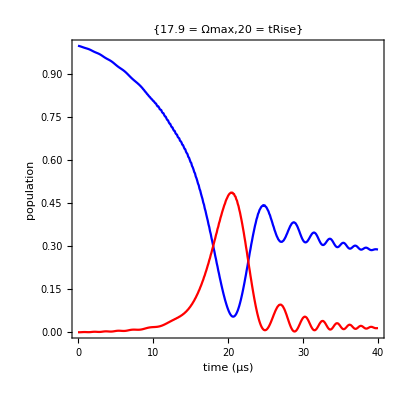
{-Graphics-,0.487566,20.7,0.443747,0.38938}

```mathematica
amplitudeARP[17.9,20]
```

```mathematica
optimaltRiseTable=Table[{Ωmax,amplitudeARP[Ωmax,20][[5]]},{Ωmax,.25,30,.25}];
```

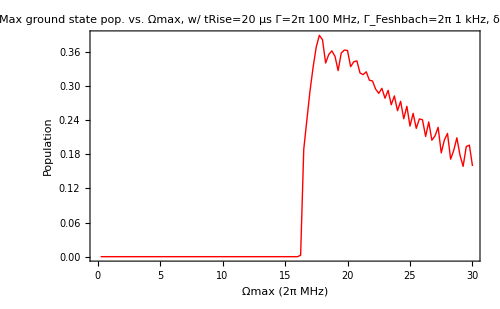

```mathematica
ListPlot[optimaltRiseTable,FrameLabel->{"Ωmax (2π MHz)","Population"},PlotLabel->"Max ground state pop. vs. Ωmax, w/ tRise=20 μs\n Γ=2π 100 MHz, Γ_Feshbach=2π 1 kHz, δ=2π 7.5 GHz",PlotRange->All]
```

```mathematica
FullSimplify[EE Exp[z/(2a)Log[F/EE]]+F Exp[-z/(2a)Log[F/EE]],Assumptions->{EE>0,F>0}]
```

(F/EE)^(-z/(2 a)) (F+EE (F/EE)^(z/a))

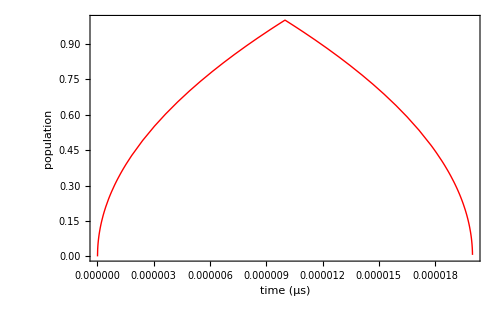

```mathematica
Plot[ Piecewise[{{√(t/(tRise μs)),t <tRise μs},{√(2 -t/(tRise μs)),t>tRise μs }}]/.{Ωmax->1,tRise->10},{t,0,30μs},PlotRange->All,FrameLabel->{"time (μs)","population"}]
```

```mathematica
D[Log[ρ[t]],t]
```

ρ'[t]/ρ[t]